## Cosmological Perturbation Theory Package

First, load the package

```mathematica
<<COSPER
```

Get::noopen: Cannot open "COSPER".

$Failed

Brief on-line help is available for all functions:

```mathematica
?IMetric
```

IMetric[g], with g an n.n-matrix (two lower indices),
  returns the inverse metric (two upper indices).

```mathematica
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

## Basic

### Background

First define the coordinate n-vector:

```mathematica
x={t,x1,x2,x3};
```

and then specify the metric as a square n×n matrix:

```mathematica
(met={{-a[t]*a[t],0,0,0},{0,a[t]*a[t],0,0},{0,0,a[t]*a[t],0},{0,0,0,a[t]*a[t]}})//MatrixForm;
```

"IMetric" is the only 1-argument function:

```mathematica
IMetric[met]//MatrixForm;
```

```mathematica
IMetric[met];
```

All other "functions" take two arguments, the metric matrix and then the coordinate vector:

```mathematica
Christoffel[met,x];
```

```mathematica
Riemann[met,x];
```

```mathematica
Ricci[met,x];
```

```mathematica
SCurvature[met,x]
```

(6 a''[t])/a[t]^3

```mathematica
FullSimplify[SCurvature[met,x]];
```

```mathematica
EinsteinTensor[met,x];
```

```mathematica
SqRicci[met,x];
```

```mathematica
SqRiemann[met,x];
```

```mathematica
(EMTensor={{-ρ[t],0,0,0},{0,p[t],0,0},{0,0,p[t],0},{0,0,0,p[t]}})//MatrixForm;
```

Friedmann Equation

```mathematica
FriedmannClassic=EinsteinTensor[met,x][[1]][[1]]==κ^2 EMTensor[[1]][[1]];
```

## ΛCDM Model

Hubble function

```mathematica
HL[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=HCurrent √(Omegam0 a^-3+Omegar0 a^-4+OmegaL);
HL1[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=D[HL[a,HCurrent,Omegam0,Omegar0,OmegaL],a];
iHL[a_]:= H0  √(Ωm0 a^-1+ Ωx0)
```

```mathematica
HL[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a,H0,Ωm0,Ωr0,Ωx0]
HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]
```

71. √(0.73+0.0000809/a^4+0.27/a^3)

(35.5 (-0.0003236/a^5-0.81/a^4))/(√(0.73+0.0000809/a^4+0.27/a^3))

-2.14831×10^9

## f(R) Gravity

f(R) signature

```mathematica
Clear[R]
RR[a_,HCurrent_,Constant_,Omegam0_,Omegar0_,mass_]=3 HCurrent^2/c^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant mass^2/c^2
D[3 HCurrent^2/lightspeed^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant mass^2/lightspeed^2,a];
RR1[a_,HCurrent_,Omegam0_,Omegar0_,mass_]=(3 HCurrent^2 (-(3 Omegam0)/a^4-(4 Omegar0)/a^5))/c^2//Simplify
```

(Constant mass^2)/45000000000+(HCurrent^2 (Omegam0/a^3+Omegar0/a^4))/30000000000

-(HCurrent^2 (3 a Omegam0+4 Omegar0))/(30000000000 a^5)

n is kinda special. Give the value of it first. Because when doing derivative

```mathematica
(*
Clear[f,fR]
(*fComp[Constant1_,Constant2_,mass_]=ffComp[4,Constant1,Constant2,mass]/.{R->R[a]};*)
f[Constant1_,Constant2_,mass_]=
fR[Constant1_,Constant2_,mass_]=ffR[1,Constant1,Constant2,mass]/.{R->R[a]}
fRR[Constant1_,Constant2_,mass_]=ffRR
*)
```

```mathematica
(*
Clear[f1,fR1,fR2]
f1[Constant1_,Constant2_,mass_]=Simplify[D[f[Constant1,Constant2,mass],a]]
fR1[Constant1_,Constant2_,mass_]=D[fR[Constant1,Constant2,mass],a]//Simplify
fR2[Constant1_,Constant2_,mass_]=D[D[fR[Constant1,Constant2,mass],a],a]
*)
```

Constants and fundamental functions. Units should be determined first.

```mathematica
Clear[Const1,Const2]
c=3*10^5;
h=0.71;
H0=100 h;
Ωx0 =0.73;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
fR0=-0.02;
d1=6 Ωx0/Ωm0;
d2=-fR0 (12/Ωm0-9)^2
m=H0 √Ωm0;
lp=√(2.47*10^-25);
Const1[nn_]=-(36(Ωx0/Ωm0)^2)/(12/Ωm0-9)^(nn+1)nn/fR0;
Const2[nn_]=-(6 Ωx0/Ωm0)/(12/Ωm0-9)^(nn+1)nn/fR0;
Ω=Ωm0 a^-3+Ωr0 a^-4;
R=RR[a,H0,d1,Ωm0,Ωr0,m];
R1=RR1[a,H0,d1,Ωm0,Ωr0,m];
(*
ρcr= (3 H0^2)/κ^2;
ρm[a_]=ρcr Ωm0 a^-3;
ρr[a_]=ρcr Ωr0 a^-4;
ρ[a_]=ρm[a]+ρr[a];
pm[a_]=0;
pr[a_]=1/3 ρr[a];
p[a_]=pm[a]+pr[a];
*)
Hubb[a_]:=HubbleL[Ωr0,Ωm0,Ωx0,H0,a];
```

25.1262

First equation: (Omega is the parameter for fraction evolution, so use )

```mathematica
f=-d1 m^2/c^2+d2 m^2/c^2 (m^2/c^2)/R
fR=-d2 m^4/c^4 1/R^2
fRR=2d2 m^4/c^4 1/R^3
3(1+fR)==3 H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3a H[a]^2 fRR R1
```

-2.45329×10^-7+(5.74648×10^-15)/(4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3))

-(5.74648×10^-15)/((4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3))^2)

(1.1493×10^-14)/((4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3))^3)

3 (1-(5.74648×10^-15)/((4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3))^2))==1/2 (2.45329×10^-7-(5.74648×10^-15)/(4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3))+(1+(5.74648×10^-15)/((4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3))^2)) (4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3)))+1.68033×10^-7 (0.0000809/a^4+0.27/a^3)-(3.44789×10^-14 a H[a]^2 RR1[a,71.,16.2222,0.27,0.0000809,36.8927])/((4.90657×10^-7+1.68033×10^-7 (0.0000809/a^4+0.27/a^3))^3)

```mathematica
Clear[H]
fRFriedmann=H[a]^2/m^2(1-d2 1/RR[a,H0,d1,Ωm0,Ωr0,m]^2)+1/6(d2 1/RR[a,H0,d1,Ωm0,Ωr0,m]-d1)+1/6 d2 1/RR[a,H0,d1,Ωm0,Ωr0,m]+2 a^2 H[a]^2/m^2 d2 1/RR[a,H0,d1,Ωm0,Ωr0,m]^3 3RR1[a,H0,Ωm0,Ωr0,m]==H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)//FullSimplify
```

-2.7037+(8.37539 a^4)/(1.35939×10^-11+4.5369×10^-8 a+4.90657×10^-7 a^4)+(0.000734716+(a^8 (-2.50952×10^-13+a (-8.43562×10^-10-1.50757×10^-8 a-9.05783×10^-9 a^3)))/((1.35939×10^-11+4.5369×10^-8 a+4.90657×10^-7 a^4)^3)) H[a]^2==(0.00029963+1. a)/a^4

```mathematica
Clear[Sol]
Sol[a_]=NDSolve[{fRFriedmann,H[10^-3]==HL[10^-3,H0,Ωm0,Ωr0,Ωx0],H'[10^-3]==HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]},H[a],{a,10^-4,1}]
```

NDSolve::ivcon: The given initial conditions were not consistent with the differential-algebraic equations. NDSolve will attempt to correct the values.

{{H[a]→InterpolatingFunction[{{0.0001,1.}},<>][a]}}

Testing Functions

```mathematica
t1=Table[i*10^-4,{i,1,10,0.1}];
t2=Table[i*10^-3,{i,1,10,0.1}];
t3=Table[i*10^-2,{i,1,10,0.1}];
t4=Table[i*10^-1,{i,1,10,0.1}];
t5=Table[i,{i,1,1,0.1}];
aTable=Join[t1,t2,t3,t4,t5];
Length[aTable]
ListPlot[aTable];
```

365

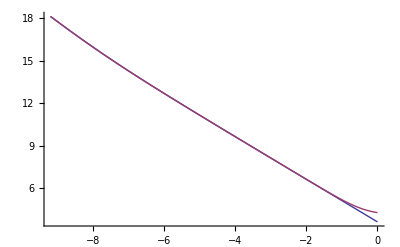

```mathematica
HubbleTable=Table[{Sol[aTable[[i]]][[1]][[1]],HL[aTable[[i]],H0,Ωm0,Ωr0,Ωx0],aTable[[i]]},{i,1,365}];
ListPlot[{Table[{Log[HubbleTable[[i]][[3]]],Log[H[HubbleTable[[i]][[3]]]/.HubbleTable[[i]][[1]]]},{i,1,365}],Table[{Log[HubbleTable[[i]][[3]]],Log[HubbleTable[[i]][[2]]]},{i,1,365}]},Joined->True]
```

ΛCDM as an example

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

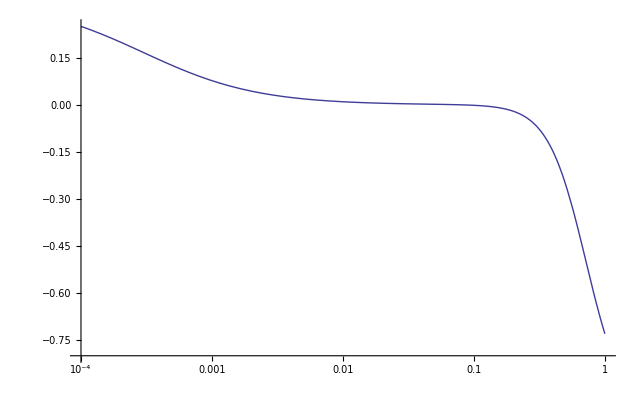

-194729.+3.56799×10^8 a^(1/9)-1.18914×10^9 a^(1/8)+1.55755×10^9 a^(1/7)-1.01651×10^9 a^(1/6)+3.45971×10^8 a^(1/5)-5.86945×10^7 a^(1/4)+4.31573×10^6 a^(1/3)-101465. √a+382.796 a

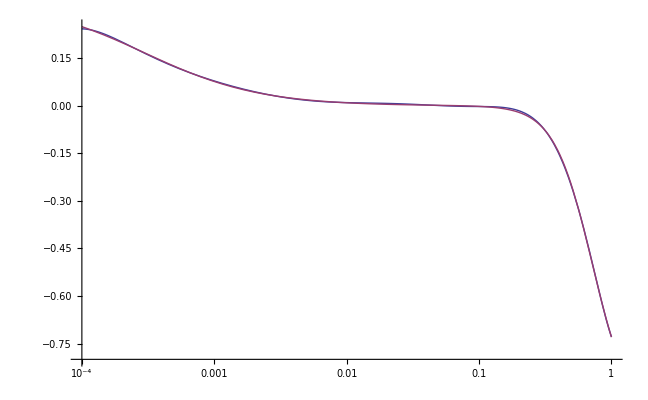

```mathematica
wleff[a_]=-1-2(a HL[a,H0,Ωm0,Ωr0,Ωx0] HL1[a,H0,Ωm0,Ωr0,Ωx0])/(3 HL[a,H0,Ωm0,Ωr0,Ωx0]^2)
LogLinearPlot[wleff[a],{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
wlefff=Table[{aTable[[i]],wleff[aTable[[i]]]},{i,1,365}];
wlefffit[a_]=Fit[wlefff,{1,a,a^(1/2),a^(1/3),a^(1/4),a^(1/5),a^(1/6),a^(1/7),a^(1/8),a^(1/9)},a]
LogLinearPlot[{wlefffit[a],wleff[a]},{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
```

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.108576} lies outside the range of data in the interpolating function. Extrapolation will be used.

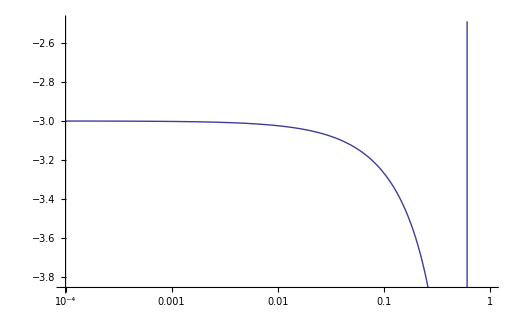

InterpolatingFunction::dmval: Input value {10000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9090.91} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-2.96909-14.664 xx+249.311 xx^2-1203.23 xx^3+1884.19 xx^4-916.806 xx^5

InterpolatingFunction::dmval: Input value {-0.108576} lies outside the range of data in the interpolating function. Extrapolation will be used.

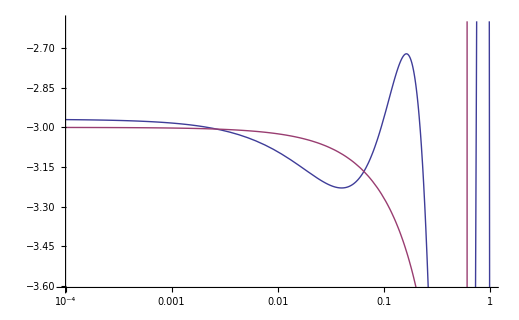

```mathematica
H1[a_]=D[H[a]/.Sol[a][[1]][[1]],a];
H[a_]=H[a]/.Sol[a][[1]][[1]];
LogLogPlot[{H[a],Abs[H1[a]]},{a,10^-4,1}];
LogLogPlot[Abs[H1[a]],{a,10^-4,1}];
weff[xx_]=-1-2(H[1/xx] H1[1/xx])/(xx 3 H[1/xx]^2);
LogLinearPlot[weff[a],{a,10^-4,1}]
wefff=Table[{aTable[[i]],weff[aTable[[i]]]},{i,1,365}];
wefffit[xx_]=Fit[wefff,{1,xx,xx^2,xx^3,xx^4,xx^5},xx]
(*wefffit[a_]=Fit[wefff,{1,a^-1,a^(-1/2),a^(-1/3),a^(-1/4),a^(-1/5)},a]*)
LogLinearPlot[{wefffit[a],weff[a]},{a,10^-4,1}]
```

```mathematica
TTT[a_]=(-d2 (1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^2))/(2d2 1/m^2 1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^3))-3 H0^2(Ωm0 a^-3+Ωr0 a^-4)-2d1 m^2)a^2
TTT[10^-3]
TTT[10^-2]
TTT[10^-1]
TTT[1]
```

(-4.91307×10^-7-7.57151×10^-9 (32.4444+9.98678×10^11 (0.0000809/a^4+0.27/a^3))-15123. (0.0000809/a^4+0.27/a^3)) a^2

-7.95999×10^6

-630833.

-61431.7

-6126.65

## f(R) Gravity Perturbation

LCDM Model data

```mathematica
Clear[GrowthL]
PowerL=Import["cdm_11-27_cut.dat"];
GrowthL[a_]:= 5/2 Ωm0  HL[a,H0,Ωm0,Ωr0,Ωx0]/H0 NIntegrate[1/(iHL[temp]/H0)^3,{temp,0,a}];
GrowthL1[a_]=D[GrowthL[a],a];
```

NIntegrate::nlim: temp = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

```mathematica
Clear[a,gg,GrowthfR,solgg]
solgg[a_]=NDSolve[{a^2 gg''[a]+(3+a/H[a] H'[a])a gg'[a]+3/2 Ωm0 (((3 H0^2/m^2 lp^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^2)/d2)gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-3]==GrowthL'[10^-3]},gg[a],{a,10^-4,1}]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{gg[a]→InterpolatingFunction[{{0.0001,1.}},<>][a]}}

{InterpolatingFunction[{{0.0001,1.}},<>][a]}

-8.56849

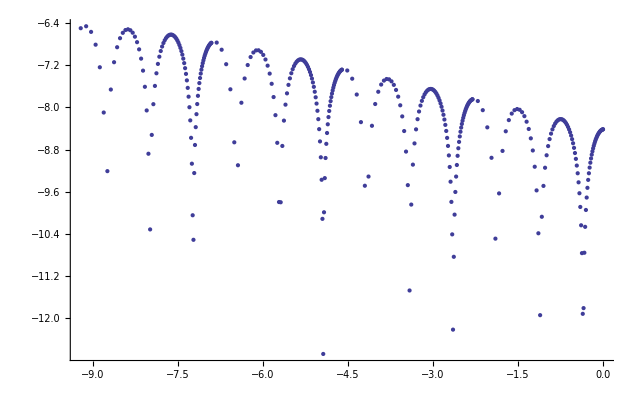

Part::partw: Part 3 of {-9.21034, -6.502} does not exist.

Part::partw: Part 3 of {-9.11503, -6.46493} does not exist.

Part::partw: Part 3 of {-9.02802, -6.57148} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {solgg} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

```mathematica
GrowthfR[a_]=gg[a]/.solgg[a]
GrowthTable=Table[{Log[aTable[[i]]],Log[Abs[GrowthfR[aTable[[i]]]]][[1]]},{i,1,365}];
GrowthTable[[10]][[1]]
ListPlot[GrowthTable]
ListPlot[{Table[{GrowthTable[[i]][[1]],GrowthTable[[i]][[2]]},{i,1,365}],Table[{GrowthTable[[i]][[1]],GrowthTable[[i]][[3]]},{i,1,365}]}];
LogLogPlot[Evaluate[gg[a]/.solgg],{x,10^-3,1},PlotRange->All]
```

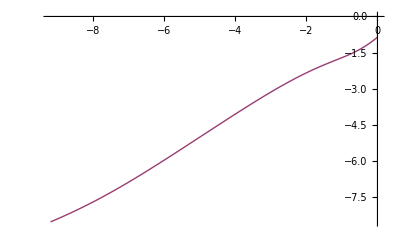

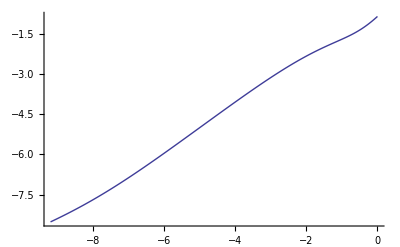

```mathematica
ListPlot[{Table[{Log[GrowthTable[[i]][[1]]],Log[GrowthTable[[i]][[2]]]},{i,1,365}],Table[{Log[aTable[[i]]],Log[GrowthL[aTable[[i]]]]},{i,1,365}]},Joined->True]
ListPlot[Table[{Log[aTable[[i]]],Log[GrowthL[aTable[[i]]]]},{i,1,365}],Joined->True]
```